```mathematica
Exit
```

```mathematica
path=FileNameJoin[{NotebookDirectory[],"submissions"}];
```

```mathematica
strm=OpenRead[path];
```

```mathematica
nextLine[]:=
Quiet@Check[
Module[{buffer,s},
buffer="";
buffer=StringJoin[buffer,Read[strm,String]];
If[buffer=="{",
s="";
While[s=!="}",
s=Read[strm,String];
buffer=StringJoin[buffer,s]
]
];
buffer
],
Close[strm];
Throw[$Failed]
]
```

```mathematica
importJSON:=Quiet[
Check[
Needs["JSONTools`"];
FromJSON,
ImportString[#,"JSON"]&
]
]
```

```mathematica
lines={};
Catch[
Module[{line},
While[StringQ[line=nextLine[]],
AppendTo[lines,importJSON[line]]
]
]
];
lines=Select[Select[lines,ListQ],("program"/.#)≠""&];
```

```mathematica
SortBy[lines,StringLength[("program"//.#)]&][[-3;;]]
```

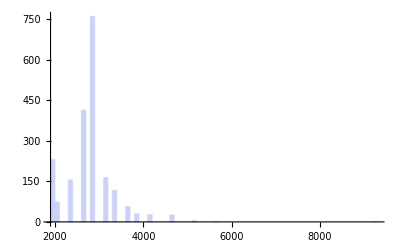

```mathematica
Histogram[ByteCount/@("program"//.lines)]
```

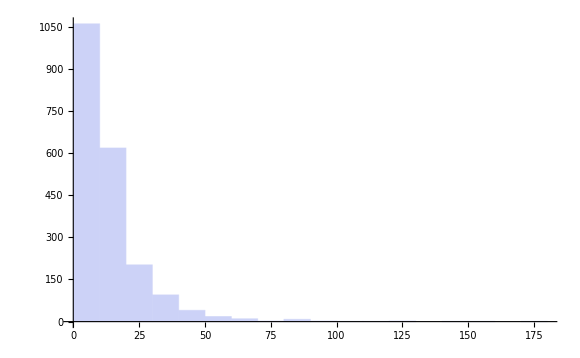

```mathematica
Histogram["attempt_count"//.lines,"Sturges"]
```